# KVADRATNA FUNKCIJA

```mathematica
Splošna oblika
```

```mathematica
Kvadratna funkcija je realna funkcija s predpisom v tako imenovani splošni obliki :
```

```mathematica
f (x)= a x^2+bx+c
```

```mathematica
kjer so koeficienti a, b in c poljubna realna števila. Koeficient a imenujemo vodilni koeficient, b koeficient linearnega člena in c prosti ali konstantni člen.
```

```mathematica
Graf kvadratne funkcije imenujemo parabola.
```

```mathematica
Obliko parabole določa vodilni koeficient a:
```

```mathematica
Če je vodilni koeficient a pozitiven (a > 0) je parabola obrnjena navzgor:
```

```mathematica
Plot[x^2, {x, -10, 10}]
```

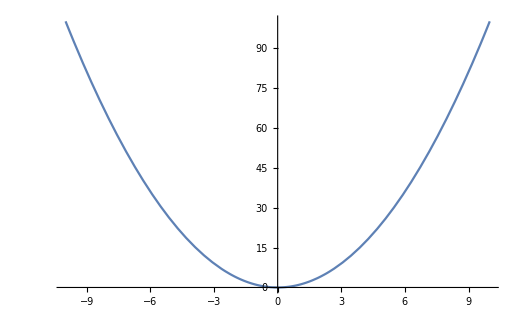

```mathematica
Če je vodilni koeficient negativen (a < 0) je parabola obrnjena navzdol:
```

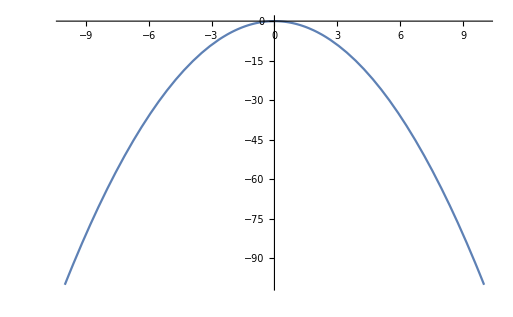

```mathematica
Plot[-x^2, {x, -10, 10}]
```

```mathematica
Širina parabole pa je odvisna od absolutne vrednosti vodilnega koeficienta. Večji kot je koeficient, bolj strma in ozka je parabola :
```

```mathematica
Manipulate[Plot[a*x^2, {x,-10, 10}, PlotRange->{0,100}],{a, 1, 10}]
```

```mathematica
Ničelna oblika
```

```mathematica
Ničelno obliko lahko zapišemo s pomočjo zapisa :
```

```mathematica
f (x)=a (x-Subscript[x, 1]) (x-Subscript[x, 2])
```

```mathematica
kjer je a vodilni koeficient in Subscript[x, 1] ter Subscript[x, 2] ničli kvadratne funkcije. Ničle so tista števila, pri katerih je vrednost funkcije f (x) enaka 0, torej seka os x.
```

```mathematica
Ničli kvadratne funkcije izračunamo po obrazcu :
```

```mathematica
Subscript[x, 1,2]=(-b±√D)/(2a)
```

```mathematica
kjer je D diskriminanta, ki jo izračunamo po obrazcu :
```

```mathematica
D = b^2 - 4a c
```

```mathematica
Za ničli kvadratne funkcije veljata tidu Vietovi formuli za vsoto in produkt ničel :
```

```mathematica
Subscript[x, 1]+Subscript[x, 2] = -b/a
	Subscript[x, 1] * Subscript[x, 2] = c/a
```

```mathematica
Če je D > 0, ima parabola dve različni realni ničli Subscript[x, 1] in Subscript[x, 2]:
```

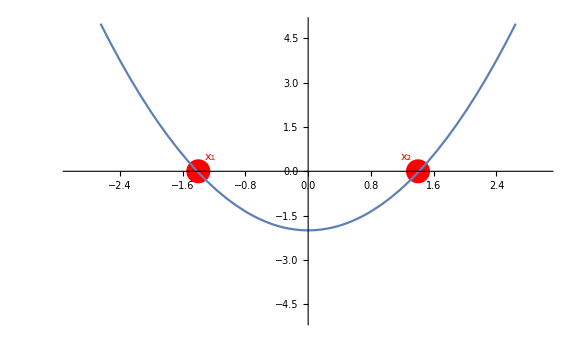

```mathematica
Plot[x^2 - 2, {x, -3, 3}, PlotRange->{-5, 5}, Prolog->{Red,PointSize[0.03], Point[{1.4, 0}],Point[{-1.4, 0}],Text[Subscript[x, 1],{-1.25,0.5}],Text[Subscript[x, 2],{1.25,0.5}]}]
```

```mathematica
Če je D  =  0, ima parabola eno dvojno realno ničlo:
```

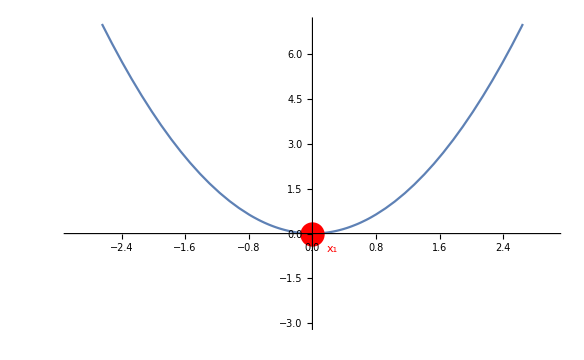

```mathematica
Plot[x^2 , {x, -3, 3}, PlotRange->{-3, 7},Prolog->{Red, PointSize[0.03], Point[{0,0}],Text[Subscript[x, 1],{0.25,-0.5}]}]
```

```mathematica
Če je D  <  0, parabola nima ničel:
```

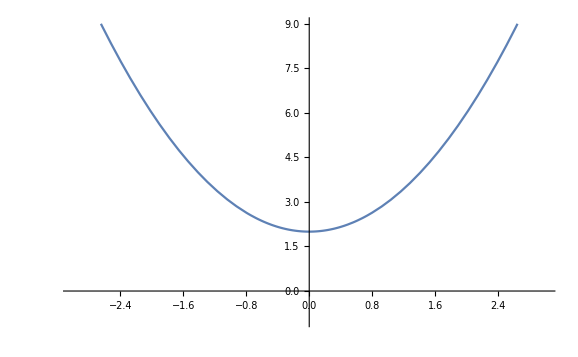

```mathematica
Plot[x^2 + 2, {x, -3, 3}, PlotRange->{-1, 9}]
```

```mathematica
Temenska oblika
```

```mathematica
Temensko obliko lahko zapišemo s pomočjo zapisa :
```

```mathematica
f(x)=a(x-p)^2+q
```

```mathematica
kjer je a vodilni koeficient in p ter q koordinati temena parabole T(p, q). Teme je točka, kjer ukrivljenost krivulje ekstremno vrednost.
```

```mathematica
Koordinati temena izračunamo z enačbama :
```

```mathematica
p=-b/(2a)
	q = -D/(4a)
```

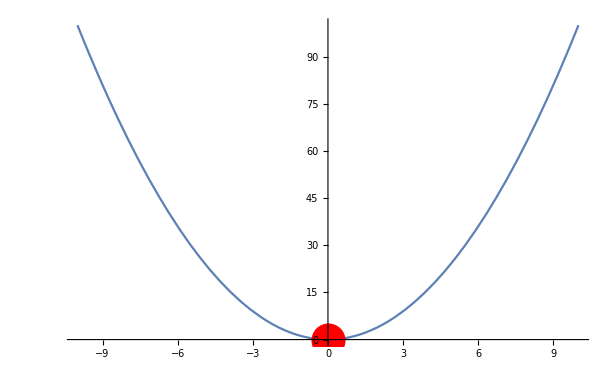

```mathematica
Plot[x^2,{x,-10, 10}, Prolog->{Red,PointSize[0.04], Point[{0,0}]}]
```

```mathematica
Graf kvadratne funkcije
```

```mathematica
Graf kvadratne funkcije lahko narišemo postopoma :
```

```mathematica
najprej narišemo graf y=x^2
```

```mathematica
nato ta graf raztegnemo v smeri osi y za faktor a
```

```mathematica
potem ga še premaknemo za vektor (p, q)
```

```mathematica
Primer 1 :
```

```mathematica
Funkcijo f (x)=2 x^2 −12 x+16 najprej preoblikujemo v temensko obliko:f (x)=2 (x-3)^2−2 in potem narišemo:
```

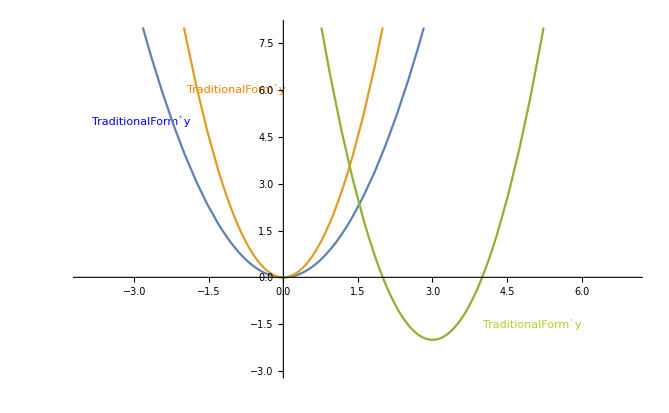

```mathematica
Plot[{{x^2},{2x^2},{2x^2-12x+16}},{x, -4, 7},PlotRange->{-3, 8},Prolog->{Blue,Text["TraditionalForm`y",{-2.85,5}],Orange,Text["TraditionalForm`y",{-0.95,6}],Blend[{Yellow, Pink, Green}],Text["TraditionalForm`y",{5,-1.5}]}]
```

```mathematica
Primer 2 :
```

```mathematica
Dana je funkcija f (x)=x^2-2x-3.
```

```mathematica
Razberemo začetno vrednost. Ta je enaka koeficientu c (f (0)=-3). Točka N(0,-3)
```

```mathematica
Funkcijo spremenimo v temensko obliko (f(x)=(x-1)^2-4) in razberemo teme:T(1, -4)
```

```mathematica
Nato moramo dobiti še ničelno obliko (f(x)=(x+1)(x-3)) in tako dobimo ničli Subscript[x, 1]=-1 in Subscript[x, 2]=3.
```

```mathematica
Narišemo graf :
```

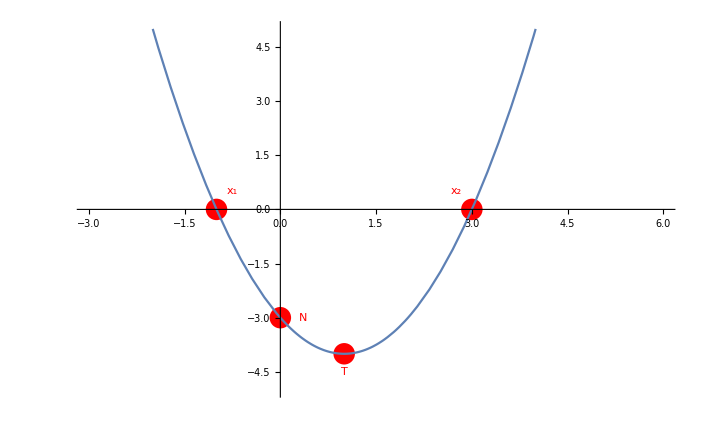

```mathematica
Plot[x^2-2x-3, {x, -3, 6}, PlotRange->{-5, 5}, Prolog->{Red, PointSize[0.022], Point[{-1,0}],Point[{3,0}],Point[{1,-4}],Point[{0,-3}], Text[Subscript[x, 1],{-0.75,0.5}],Text[Subscript[x, 2],{2.75,0.5}],Text[T,{1,-4.5}],Text[N,{0.35,-3}]}]
```